```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];

enzModelsDir = "/home/mrama/Dropbox/MASSef/examples/"
mainDir=enzModelsDir<>"code_data/";
Import[mainDir<>"sim_plot_functions.m"];
Import[mainDir<>"simulation.m"];
```

/home/mrama/Dropbox/MASSef/examples/

## Simulations

### Systematic simulations

```mathematica
modelList=Import["/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/model_simulations/models/model_FBA1_p2_keq_1_1.mx", "MX"];
```

```mathematica
Length@modelList
```

50

```mathematica
(Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, TPI1]^⟶,Subscript[k, TPI2]^⟶,Subscript[k, TPI3]^⟶}])/
(Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, TPI1]^⟵,Subscript[k, TPI2]^⟵,Subscript[k, TPI3]^⟵}])
```

9.35

```mathematica
modelList=Delete[modelList,{10}];
```

```mathematica
Export["/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/model_simulations/models/model_FBA1_p2_keq_1_1.mx",modelList, "MX"];
```

```mathematica
Do[
Print[i];
simulate[modelList[[i]],{t,0,tFinal}],
{i, 1, Length@modelList}]
```

```mathematica
modelList[[1]]["InitialConditions"]
```

{(13dpg)^c→0.0000165 Mole Liter^-1,(23dpg)^c→0.0000829 Mole Liter^-1,(2pg)^c→0.0000918 Mole Liter^-1,(3pg)^c→0.00154 Mole Liter^-1,adp^c→0.000555 Mole Liter^-1,amp^c→0.000281 Mole Liter^-1,atp^c→0.00963 Mole Liter^-1,e4p^c→0.000049 Mole Liter^-1,f6p^c→0.00252 Mole Liter^-1,g6p^c→0.00788 Mole Liter^-1,mg2^c→0.0239 Mole Liter^-1,nad^c→0.00255 Mole Liter^-1,nadh^c→0.0000836 Mole Liter^-1,pep^c→0.000184 Mole Liter^-1,pi^c→0.0239 Mole Liter^-1,pyr^c→0.00366 Mole Liter^-1,s7p^c→0.000882 Mole Liter^-1,(FBA1^c)_^→1.05741×10^-11 Mole Liter^-1,(FBA1^c&cit^c)_^→9.19588×10^-11 Mole Liter^-1,(FBA1^c&dhap^c)_^→1.58657×10^-9 Mole Liter^-1,(FBA1^c&fdp^c)_^→1.18847×10^-7 Mole Liter^-1,(FBA1^c&cit^c&dhap^c)_^→9.88607×10^-7 Mole Liter^-1,(FBA1^c&cit^c&fdp^c)_^→1.08564×10^-8 Mole Liter^-1,(FBA1^c&dhap^c&g3p^c)_^→1.13107×10^-13 Mole Liter^-1,(FBA1^c&cit^c&dhap^c&g3p^c)_^→6.98655×10^-14 Mole Liter^-1,cit^c→0.001959,cit_total_Global→0.00196,dhap^c→0.00305901,dhap_total_Global→0.00306,fdp^c→0.0151999,fdp_total_Global→0.0152,g3p^c→0.000271,g3p_total_Global→0.000271}

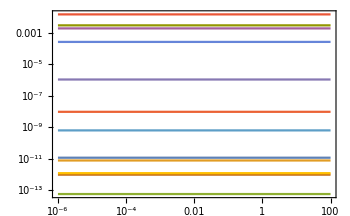

```mathematica
tFinal=100;
{conc,flux}=simulate[modelList[[50]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}]
```

```mathematica
modelList[[1]]["Species"]
```

{(TPI^c)_^,(TPI^c&dhap^c)_^,dhap^c,g3p^c,(TPI^c&g3p^c)_^}

```mathematica
Values@FilterRules[conc/.t-> tFinal, dhap^c]/Values@FilterRules[conc/.t-> tFinal, g3p^c]
```

{9.35}

```mathematica
flux//Keys
```

{v_FBA11,v_FBA12,v_FBA13,v_FBA14,v_FBA15,v_FBA16,v_FBA17,v_FBA18,v_FBA19}

```mathematica
conc//Keys
```

{(FBA1^c)_^,(FBA1^c&cit^c)_^,(FBA1^c&dhap^c)_^,(FBA1^c&fdp^c)_^,(FBA1^c&cit^c&dhap^c)_^,(FBA1^c&cit^c&fdp^c)_^,(FBA1^c&dhap^c&g3p^c)_^,(FBA1^c&cit^c&dhap^c&g3p^c)_^,cit^c,dhap^c,fdp^c,g3p^c}

```mathematica
Keys[conc][[9]]
```

cit^c

```mathematica
enzName="FBA1";
inputDir = enzModelsDir<>"FBA1/fit_FBA1/output/model_simulations/models/";
outputDirBase = enzModelsDir<>"FBA1/fit_FBA1/output/model_simulations/data/";
If[!DirectoryQ[outputDirBase],
	CreateDirectory[outputDirBase,CreateIntermediateDirectories-> True]
];

headerConcMets={"fdp","dhap","g3p"};
headerConcEnz={"FBA1","FBA1","FBA1","FBA1","FBA1","FBA1","FBA1","FBA1"};
headerFlux={"v_FBA1","v_FBA1","v_FBA1", "v_FBA1","v_FBA1","v_FBA1","v_FBA1","v_FBA1","v_FBA1"};
subInd = {11};
prodInd={10,12};
indEnz=Range[8];

initCondList={};
outputDirList={"noPerturb"};


tValues=Map[10^#&,Range[-6,2, 0.1]];
tFinal=100;
tValues=Insert[tValues,0., 1];


modelIDList={"p2_keq_1"};
nModelEnsembles={0,2};

 

outputDir =outputDirBase;
If[!DirectoryQ[outputDir<>"/data_mx/"],
	CreateDirectory[outputDir<>"/data_mx/",CreateIntermediateDirectories-> True]
];
```

```mathematica
Do[

simulateEnsembleNoCheck[inputDir, outputDir, enzName, modelID, nModelEnsembles, tFinal, tValues, initCondList, headerConcEnz, headerConcMets, headerFlux, indEnz,subInd, prodInd];,

{modelID, modelIDList}];
```

/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/model_simulations/models/model_FBA1_p2_keq_1_0.mx

/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/model_simulations/models/model_FBA1_p2_keq_1_1.mx

/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/model_simulations/models/model_FBA1_p2_keq_1_2.mx